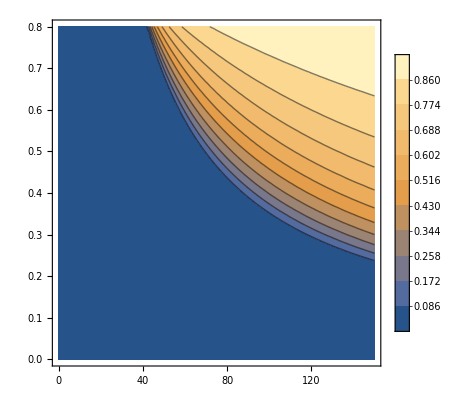

```mathematica
k=4.5;
ff[Pe_,phi_]:=(4 phi Pe-3Pi^2 k )/(4 phi Pe-6 k Pi 3^(1/2)phi)
f[Pe_,phi_] := If[Pe>3 Pi^2 k/(4 phi),ff[Pe,phi],0];
ContourPlot[f[Pe,phi],{Pe,0,150},{phi,0,0.8},Contours->10,ContourLabels->False,PlotLegends->Automatic,Exclusions->None]
```

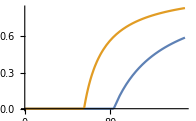

```mathematica
Plot[{f[Pe,.4],f[Pe,.6]},{Pe,0,150}]
```

```mathematica
(* Blue with phi=0.4.  Shows binodal at set system density *)
```